#### Fabry-Perot Etalon1 (wavelength,angle)

frs = 1.45631×10^13(Hz), fwhm = 1.65161×10^11, Finesse = 88.175

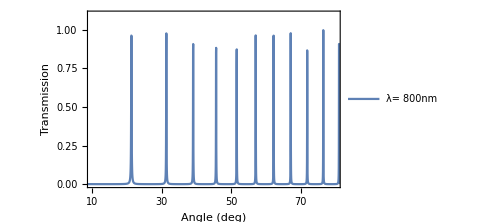
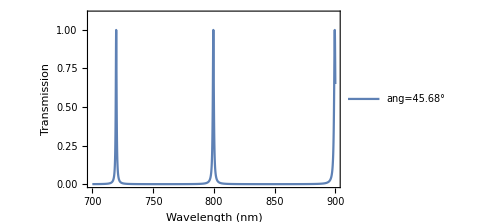
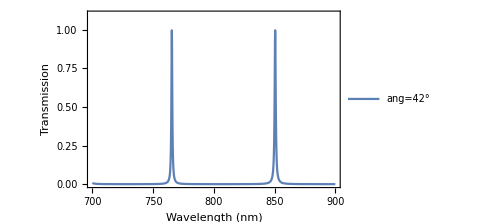

-Graphics-

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

c=3 10^8;(*m/s*)
n=1;(*air gap etalon*)
d=0.0103*10^-3;(*m, effective thickness*)
(*λ=800 10^-9;*) (*m*)
(*θ=ang in degree*)
R=0.965;(*dd*)
fsr=c/(2n d);(*Hz*)
fwhm=(c (1-R))/(2π n d √R);(*Hz*)
F=(π √R)/(1-R);
Print["frs = ",fsr,"(Hz), fwhm = ",fwhm,", Finesse = ",F]

δ[λ_,θ_]:=(2π)/λ n d Cos[θ π/180];
T[λ_,θ_]:=1/(1+(4R)/(1-R)^2 Sin[δ[λ,θ]/2]^2);
λ1=800 10^-9 ;(*m*)
p1=Plot[T[λ1,θ],{θ,0,90},PlotRange->{{10,80},{0,1.1}},PlotLegends->Placed[{"λ= 800nm"},{0.15,0.95}],Frame->True,FrameLabel->{"Angle (deg)","Transmission"},ImageSize->Medium,LabelStyle->{FontFamily->"Arial", FontSize->12,Black},FrameTicks->{{Automatic,None},{Table[λ,{λ,10,80,10}],None}}];

ang=45.68;(*deg*)
p2=Plot[T[λ,ang],{λ,700 10^-9,900 10^-9},PlotRange->{{700 10^-9,900 10^-9},{0,1.1}},PlotLegends->Placed[{"ang=45.68°"},{0.15,0.95}],Frame->True,FrameLabel->{"Wavelength (nm)","Transmission"},ImageSize->Medium,LabelStyle->{FontFamily->"Arial", FontSize->12,Black},FrameTicks->{{Automatic,None},{Table[{λ*10^-9,λ},{λ,700,900,50}],None}}];

ang=42 ;(*deg*)
p3=Plot[T[λ,ang],{λ,700 10^-9,900 10^-9},PlotRange->{{700 10^-9,900 10^-9},{0,1.1}},PlotLegends->Placed[{"ang=42°"},{0.15,0.95}],Frame->True,FrameLabel->{"Wavelength (nm)","Transmission"},ImageSize->Medium,LabelStyle->{FontFamily->"Arial", FontSize->12,Black},FrameTicks->{{Automatic,None},{Table[{λ*10^-9,λ},{λ,700,900,50}],None}}];

{p1,p2,p3}

p4=Plot3D[T[λ,θ],{λ,700 10^-9,900 10^-9},{θ,10,80},PlotRange->All,PlotLegends->Placed[{"T(λ,θ)"},{0.1,0.85}],ImageSize->Large,LabelStyle->{FontFamily->"Arial", FontSize->12,Black},LabelStyle->{FontFamily->"Arial",FontSize->12,Black},AxesLabel->{"Wavelength (nm)","Angle (°)","Transmission"}]
```

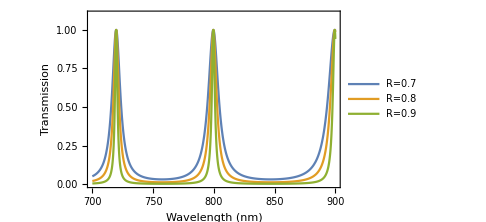

```mathematica
ang=45.68;(*deg*)
ClearAll[R];
T[λ_,θ_]:=1/(1+(4R)/(1-R)^2 Sin[δ[λ,θ]/2]^2);
Plot[{T[λ,ang]/.R->{0.7},T[λ,ang]/.R->{0.8},T[λ,ang]/.R->{0.9}},{λ,700 10^-9,900 10^-9},PlotRange->{{700 10^-9,900 10^-9},{0,1.1}},PlotLegends->Placed[{"R=0.7","R=0.8","R=0.9"},{0.3,0.7}],Frame->True,FrameLabel->{"Wavelength (nm)","Transmission"},ImageSize->Medium,LabelStyle->{FontFamily->"Arial", FontSize->12,Black},FrameTicks->{{Automatic,None},{Table[{λ*10^-9,λ},{λ,700,900,50}],None}}]
```